```mathematica
m:=2
d:=3
l:=1
Subscript[m, c]:=Sqrt[3]/2
M:= Sqrt[m^2+Subscript[m, c]^2]
d:=3
H1=(d-1)/2+Sqrt[((d-1)/2)^2-M^2 l^2];
H2=(d-1)/2-Sqrt[((d-1)/2)^2-M^2 l^2];
norm=Gamma[H1]*Gamma[H2]/((4*π)^(d/2)*l^2*Gamma[d/2]);
W[τ_]:=norm*Hypergeometric2F1[H1,H2,d/2,1/2*(1+Cosh[τ])]
Wpodal[τ_]:=norm*Hypergeometric2F1[H1,H2,d/2,1/2*(1-Cosh[τ])]
Walpha[τ_,α_,β_]:= Cosh[2α]*W[τ]+Sinh[2α]*(Cos[β]*Re[Wpodal[τ]]-Sin[β]*Im[Wpodal[τ]])

Δ[τ_]:= Cos[m τ]/(2 π τ)
```

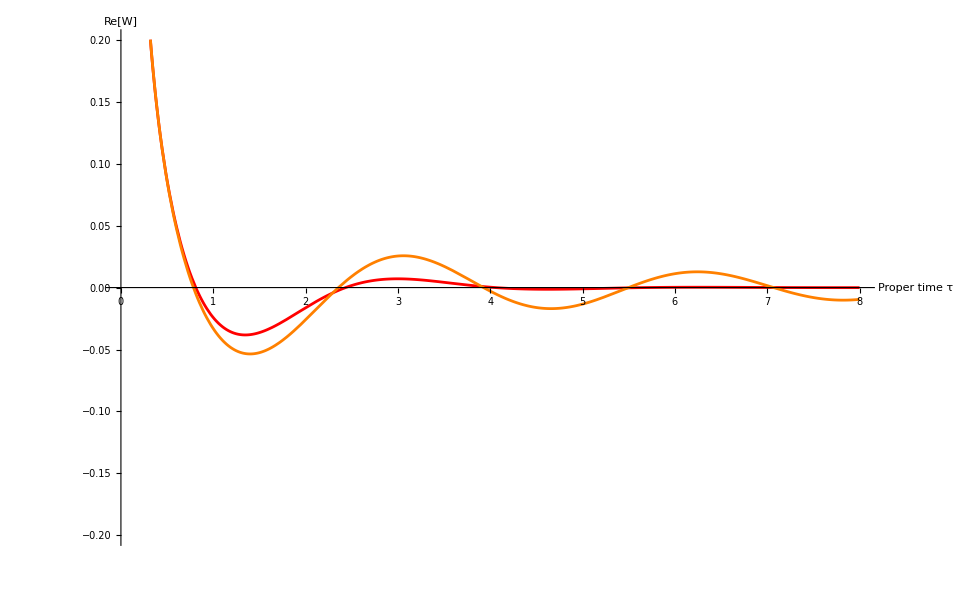

```mathematica
plotLength:=8;
Show[Plot[-Im[W[τ]],{τ,0,plotLength},PlotStyle->Red,PlotRange->{{0,plotLength},{-.2,.2}}],
Plot[1/2 Δ[τ],{τ,0,plotLength},PlotStyle->Orange,PlotRange->{{0,plotLength},{-.2,.2}}],
AxesOrigin->{0,0},PlotRange->{{0,plotLength},{-.2,.2}},AxesLabel->{"Proper time τ","Re[W]"}]
```

```mathematica
N[Limit[Im[norm*Hypergeometric2F1[H1,H2,d/2,1/2*(1+Cosh[1]+I*ϵ)]],{ϵ->0}]]
Im[W[2]]
```

Indeterminate

Indeterminate